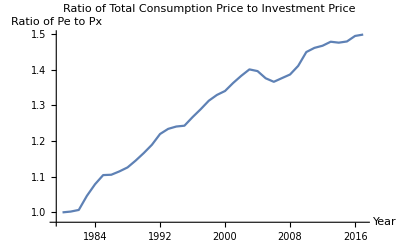

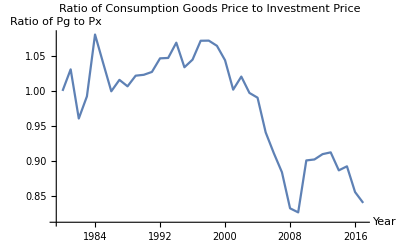

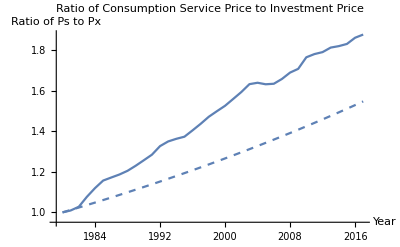

```mathematica
(* prices *)

prices={{"year","consumption","goods cons.","services cons.","investment"},{1980,3.38486,2.49874,4.27722,3.70660},{1981,3.70706,2.81452,4.71789,4.05046},{1982,3.94020,2.77526,5.08145,4.28557},{1983,4.13014,2.89092,5.37101,4.32213},{1984,4.30928,3.18558,5.65199,4.37383},{1985,4.47032,3.10615,5.91693,4.43179},{1986,4.56129,3.04405,6.11072,4.51800},{1987,4.68333,3.14970,6.29964,4.59972},{1988,4.85947,3.20651,6.57150,4.72555},{1989,5.06906,3.33837,6.87916,4.84678},{1990,5.27972,3.41825,7.19019,4.95664},{1991,5.48049,3.49304,7.47847,5.04494},{1992,5.63350,3.56772,7.74407,5.05738},{1993,5.78062,3.62014,7.99018,5.12893},{1994,5.91037,3.75824,8.20389,5.21613},{1995,6.03666,3.70584,8.42766,5.31778},{1996,6.17206,3.75615,8.64583,5.33394},{1997,6.30188,3.86652,8.87597,5.35258},{1998,6.39851,3.85496,9.06244,5.33572},{1999,6.50663,3.84563,9.27319,5.35980},{2000,6.66676,3.83200,9.58983,5.44609},{2001,6.84303,3.71272,9.89450,5.49755},{2002,6.97210,3.79725,10.15155,5.51994},{2003,7.12951,3.74572,10.49883,5.57243},{2004,7.31532,3.83041,10.85537,5.73742},{2005,7.52009,3.79532,11.27063,5.98417},{2006,7.73929,3.81063,11.70145,6.20323},{2007,7.96210,3.77461,12.12070,6.33387},{2008,8.12778,3.60227,12.51524,6.41826},{2009,8.20824,3.55071,12.55769,6.37067},{2010,8.34884,3.82982,12.84648,6.30640},{2011,8.53499,3.88994,13.14500,6.39552},{2012,8.70147,3.98272,13.41895,6.49351},{2013,8.86704,4.03900,13.74033,6.56695},{2014,9.02963,4.00448,14.07275,6.69924},{2015,9.12429,4.06337,14.27155,6.75385},{2016,9.23528,3.90288,14.53424,6.76541},{2017,9.41576,3.89692,14.90486,6.87951}};

yearCTotPData=prices[[All,{1,2}]];

(*Use ListPlot to plot the data*)
ListPlot[yearCTotPData,Joined->True,AxesLabel->{"Year","Total Consumption Price Index"},PlotLabel->"Total Consumption Price Index Over Years"];

(*Calculate the ratios*)
constoinv=(#[[2]]/#[[5]])&/@prices prices[[2,5]]/prices[[2,2]];
goodstoinv=(#[[3]]/#[[5]])&/@prices prices[[2,5]]/prices[[2,3]];
servtoinv=(#[[4]]/#[[5]])&/@prices prices[[2,5]]/prices[[2,4]];

(*Create year-ratio pairs*)
pairsconstoinv=MapThread[{#1[[1]],#2}&,{prices,constoinv}];
pairsgoodstoinv=MapThread[{#1[[1]],#2}&,{prices,goodstoinv}];
pairsservtoinv=MapThread[{#1[[1]],#2}&,{prices,servtoinv}];

(*Plot the ratios over the years*)
expfig=ListPlot[pairsconstoinv,Joined->True,AxesLabel->{"Year","Ratio of Pe to Px"},PlotLabel->"Ratio of Total Consumption Price to Investment Price"]
goodsfig=ListPlot[pairsgoodstoinv,Joined->True,AxesLabel->{"Year","Ratio of Pg to Px"},PlotLabel->"Ratio of Consumption Goods Price to Investment Price"]
servsfig=ListPlot[pairsservtoinv,Joined->True,AxesLabel->{"Year","Ratio of Ps to Px"},PlotLabel->"Ratio of Consumption Service Price to Investment Price"];

sermodel=Plot[Ps[t],{t,1980,2017},PlotStyle->{Dashed}];

Show[servsfig,sermodel]
```